BLER α-μ:

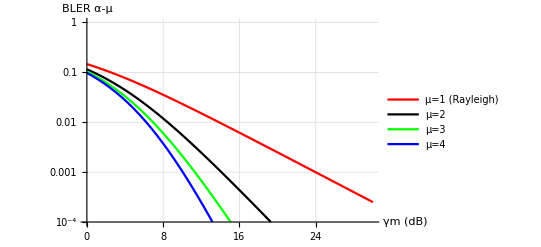

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];fαμ[γ_,γm_,μ_]:= (μ^μ γ^(μ -1))/((10^(γm/10))^μ Gamma[μ])Exp[-(μ γ)/10^(γm/10)];pdfω[γ_,γm_,α_,μ_]:=(ⅇ^(-μ γ^(α/2) ((μ^(2/α) (10^(γm/10)) Gamma[μ])/Gamma[2/α+μ])^(-α/2)) α μ^μ γ^(-1+(α μ)/2) ((μ^(2/α) (10^(γm/10)) Gamma[μ])/Gamma[2/α+μ])^(-(α μ)/2))/(2 Gamma[μ]);probErrorPSK[γ_]:=Q[√(2 γ)];BERBPSK[γm_,α_,μ_] := Re[Integrate[probErrorPSK[γ]×pdfω[γ, γm,α,μ], {γ,0,∞}]];PNmPSK[γm_,α_,μ_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERBPSK[γm,α,μ])^(N-m)×(BERBPSK[γm,α,μ])^m;PeMPSK[γm_,α_,μ_,N_]:= 1 - PNmPSK[γm,α,μ,N,0];LogPlot[{PeMPSK[γm,2,1,1], PeMPSK[γm,2,2,1], PeMPSK[γm,2,3,1], PeMPSK[γm,2,4,1]},{γm,0,30},AxesLabel->{"γm (dB)","BLER α-μ"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black, Green, Blue},PlotLegends->{"μ=1 (Rayleigh)","μ=2","μ=3","μ=4"},GridLines->Automatic]
```

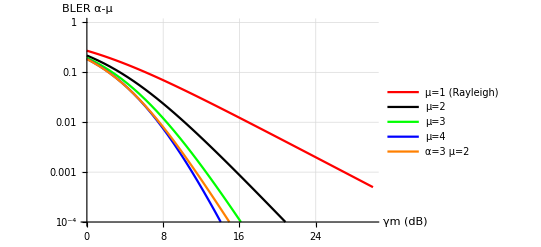

```mathematica
LogPlot[{PeMPSK[γm,2,1,2], PeMPSK[γm,2,2,2], PeMPSK[γm,2,3,2], PeMPSK[γm,2,4,2], PeMPSK[γm,3,2,2]},{γm,0,30},AxesLabel->{"γm (dB)","BLER α-μ"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black, Green, Blue, Orange},PlotLegends->{"μ=1 (Rayleigh)","μ=2","μ=3","μ=4","α=3 μ=2"},GridLines->Automatic]
```

```mathematica
N[ⅇ]
```

2.71828